```mathematica
Quit[];
```

```mathematica
mmu=MaxMemoryUsed[]
SetDirectory[NotebookDirectory[]];
(* Global Properties *)
eV=27.211;
h=4.135667516×10^-15;
c=3×10^8;
shell={"s","p","p+","d","d+","f","f+","g","g+"};
RelOrbitals={"4s","5s","4p","4p+","5p","5p+","4d","4d+","5d","5d+","4f","4f+","5f","5f+","5g","5g+"};
jOrbitals={0.5,0.5,0.5,1.5,0.5,1.5,1.5,2.5,1.5,2.5,2.5,3.5,2.5,3.5,3.5,4.5};
(* s must ne first; nj, nj+ must be consecutive *) 
NonRelOrbitals={"4s","5s","4p","5p","4d","5d","4f","5f","5g"};
l={0,0,1,1,2,2,3,3,4};
MaxElectrons=2(2l+1);
spin={0.5,-0.5};

<<ReadAMBiTOutput`;
<<MBQCSpectra`;

FS=14; FF="Helvetica"; (* Plotting Font Size and Font*)
ImRes=600; (* Export Image Resolution dpi *)
```

90595896

```mathematica
NoCIEnergies[fileMBQC_,G_]:=Module[{Shells,EnergyCSF,Num,L,TotalLines,NumTotal,Cutoff,increment,max,min,z,Density,Emin,PsiE},
{
{Shells,EnergyCSF,Num}=ReadLevels[fileMBQC];
L=Length[Shells];
TotalLines=L*(L-1)/2;
EnergyCSF=EnergyCSF eV;
Print["# of CSF averaged states: ",L];
NumTotal=Total[Num];


Cutoff=G; (*Lorenzian has range 2*Cutoff *)
increment=0.005;
max=Max[EnergyCSF]+Cutoff+10;
min=Floor[Min[EnergyCSF]-Cutoff-10];
{z,Density}=LevelDensity[EnergyCSF,Num,G,increment,max,min,Cutoff];

{Emin,PsiE}=ComplexWaveEnergies[G,z,Density,increment,EnergyCSF,Num];
PsiE=PsiE-Emin;
z=z-Emin;
EnergyCSF=EnergyCSF-Emin;
(*EnergyCSF=EnergyCSF-Min[EnergyCSF];*)
};
Return[{L,TotalLines,EnergyCSF,Shells,Num,z,Density}]
]
EigVal[V2_,j_,EnergyCSF_]:=Module[{Eig,M,i},
{
SeedRandom[j];
M=RandomVariate[NormalDistribution[0,V2],{L,L}];
M=(M+Mᵀ)/2;
For[i=1,i≤L,i++,
{
M[[i,i]]=EnergyCSF[[i]];
}];
Eig=Eigenvalues[M];
};
Return[Eig] ;
]

CIEnergies[V2_,EnergyCSF_,G_,MonteCarlo_,Num_,L_]:=Module[{increment,Cutoff,Eig,mean,EnergyCI,max,min,zCI,DensityCI,EminCI,PsiECI,Dspacing},
{
increment=0.005;
Cutoff=G;
Eig=Table[EigVal[V2,i,EnergyCSF],{i,1,MonteCarlo}];
mean=Mean[Eig];
EnergyCI=mean[[Ordering[mean]]];
max=Max[EnergyCI]+Cutoff+10;
min=Floor[Min[EnergyCI]-Cutoff-10];
{zCI,DensityCI}=LevelDensity[EnergyCI,Num,G,increment,max,min,Cutoff];
{EminCI,PsiECI}=ComplexWaveEnergies[G,zCI,DensityCI,increment,EnergyCI,Num];
PsiECI=PsiECI-EminCI;
zCI=zCI-EminCI;
EnergyCI=EnergyCI-EminCI;
(*PsiECI=PsiECI-Min[EnergyCI];
zCI=zCI-Min[EnergyCI];
EnergyCI=EnergyCI-Min[EnergyCI];
EminCI=Min[PsiECI];*)
Dspacing=Table[LevelSpacing[PsiECI,EnergyCI[[i]],G],{i,1,L}];
};
Return[{EnergyCI,Dspacing,zCI,DensityCI,EminCI}]
]

PartitionValue[EnergyCI_,Temp_,Num_,L_,EminCI_]:=Module[{Z},
{
Z=Total[Table[Num[[i]]*Exp[-(EnergyCI[[i]](*-EminCI*))/Temp],{i,1,L}]];
};
Return[Z]
]

StatisticalValues[G_,EnergyCI_,EnergyCSF_,Num_,Shells_,L_]:=Module[{Components,Components2,CONFIGS,NumPROJECT,NonRelConfigs,NumCONFIGS,RelConfigs,AverageJ,AverageJall,i,pos,Jinitial,nAverage},
{
Components=ComplexCoefficients2[G,EnergyCI,EnergyCSF,Num,2*G];
Components2=Components^2;
{CONFIGS,NumPROJECT,NonRelConfigs,NumCONFIGS,RelConfigs}=NonRelativisticConfiguration[Shells,Num];
AverageJ=ConigurationAverageJ[CONFIGS];
AverageJall=ConstantArray[0,Length[NonRelConfigs]];
For[i=1,i≤Length[CONFIGS],i=i+1,
{
pos=Position[NonRelConfigs,CONFIGS[[i]]];
AverageJall[[posᵀ[[1]]]]=AverageJ[[i]];
}];
Jinitial=Table[Total[AverageJall*Components[[i]]]/Total[Components[[i]]],{i,1,L}];
nAverage=(RelConfigsᵀ/(2*jOrbitals+1))ᵀ;

};
Return[{Components2,Jinitial,nAverage}]
]
EnergyImages[EnergyCI_,EnergyCSF_,L_]:=Module[{imEn,i,s1,EnergyCI2,EnergyCSF2},
{
EnergyCI2=EnergyCI(*-Min[EnergyCI]*);
EnergyCSF2=EnergyCSF(*-Min[EnergyCSF]*);
imEn={};
For[i=1,i≤L,i++,
{
AppendTo[imEn,ListPlot[{{EnergyCSF2[[i]],0.05},{EnergyCSF2[[i]],0.45}},PlotStyle->Black,Joined->True]];
AppendTo[imEn,ListPlot[{{EnergyCI2[[i]],0.55},{EnergyCI2[[i]],0.95}},PlotStyle->Blue,Joined->True]]
}];
s1=Show[imEn,AspectRatio->1/3,ImageSize->Large,PlotRange->All]
};
Return[s1]
]
```

# Code Starts Here

```mathematica
ION="12";
configs="df-df-0";
filenameMBQC="E1_Transitions3/Sn"<>ION<>"_0/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
fileMBQC=Import[filenameMBQC,"CSV"];
filenameCI="E1_Transitions3/Sn"<>ION<>"/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
fileCI=Import[filenameCI,"CSV"];
(*filename0diag="E1_Transitions3/Sn"<>ION<>"_0/"<>configs<>"/Sn"<>ION<>"+_E1.txt";*)
file0diag=(*Import[filename0diag,"CSV"];*)fileMBQC;
```

# of CSF averaged states: 42

Total number of MBQC Lines = 861

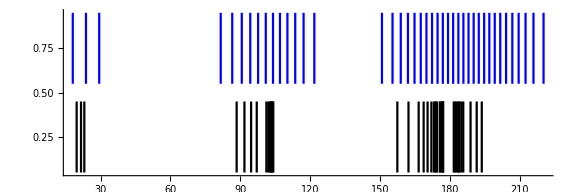

```mathematica
(* Sn08 -> 15, Sn09 -> 16, Sn10 -> 17, Sn11 -> 20, Sn12 -> 22, Sn13 -> 23, Sn14 -> 24*)
G=22;
Temp=26;
{L,TotalLines,EnergyCSF,Shells,Num,z,Density}=NoCIEnergies[fileMBQC,G];
Print["Total number of MBQC Lines = ",TotalLines]
T=SingleTransitionData[fileMBQC];
Ltran=Length[T];
If[configs=="d-0",V=2.5];
If[configs=="f-0",V=1.6];
If[configs=="df-0",V=2];
If[configs=="df-df-0",V=2.2];
If[configs=="df-df-df-0",V=1.5];
If[configs=="Range2",V=0.61];
V2=V^2;
MonteCarlo=1000;
{EnergyCI,Dspacing,zCI,DensityCI,EminCI}=CIEnergies[V2,EnergyCSF,G,MonteCarlo,Num,L];
EnergyImages[EnergyCI,EnergyCSF,L]
Z=PartitionValue[EnergyCI,Temp,Num,L,EminCI];
{Components2,Jinitial,nAverage}=StatisticalValues[G,EnergyCI,EnergyCI(*EnergyCSF*),Num,Shells,L];
E1=Table[E1Transitions[i,j,Shells,T,nAverage],{i,1,L},{j,1,L}];
indicies=ListIndicies[L];
```

```mathematica
fCI=ReadCI[fileCI];
EnergyfCI=Flatten[fCI[[All,All,4,All,2]]];
EnergyfCI=EnergyfCI-Min[EnergyfCI];
EnergyfCI=EnergyfCI*27.211;
fNoCI=ReadCI[file0diag];
EnergyfNoCI=Flatten[fNoCI[[All,All,4,All,2]]];
EnergyfNoCI=EnergyfNoCI-Min[EnergyfNoCI];
EnergyfNoCI=EnergyfNoCI*27.211;
imNoCI={}
imCI={}
For[i=1,i≤Length[EnergyfCI],i++,
{
AppendTo[imNoCI,ListPlot[{{EnergyfNoCI[[i]],0.05},{EnergyfNoCI[[i]],0.45}},PlotStyle->Black,Joined->True]];
AppendTo[imCI,ListPlot[{{EnergyfCI[[i]],1.05},{EnergyfCI[[i]],1.45}},PlotStyle->Blue,Joined->True]]
}];

imAvNoCI={};
imAvCI={};
For[i=1,i≤L,i++,
{
AppendTo[imAvNoCI,ListPlot[{{EnergyCSF[[i]]-Min[EnergyCSF],0.55},{EnergyCSF[[i]]-Min[EnergyCSF],0.95}},PlotStyle->{Black,Dashed},Joined->True,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->1/3]];
AppendTo[imAvCI,ListPlot[{{EnergyCI[[i]]-Min[EnergyCI],1.55},{EnergyCI[[i]]-Min[EnergyCI],1.95}},PlotStyle->{Blue,Dashed},Joined->True,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->1/3]]
}];
```

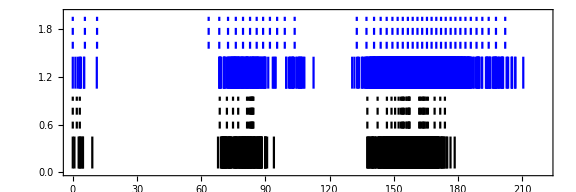

```mathematica
Show[{imNoCI,imCI,imAvNoCI,imAvCI},Frame->{True,False,False,False},PlotRangePadding->0,FrameLabel->{"E (eV)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],PlotRange->{{0,220},{0,2}},AspectRatio->1/3]
```